# Progressive strain analysis of a plane This notebook is an application example of the software StrainModeler developed in the paper:

StrainModeler: A Mathematica-based program for 3D analysis of finite and progressive strain

Nilo C. Bobillo-Ares (a), Jesús Aller (b), Fernando Bastida (b), Omar Menéndez (a), Richard J. Lisle (c)

(a) Departamento de Matemáticas, Universidad de Oviedo, 33007 Oviedo, Spain
(b) Departamento de Geología, Universidad de Oviedo, Jesús Arias de Velasco s/n, 33005 Oviedo, Spain
(c) School of Earth and Ocean Sciences, Cardiff University, Cardiff CF10 3AT, UK

1. Before executing this notebook you must open the notebook StrainModeler.nb (see the workflow in the companion Readme file). The following message pops up:

“Do you want to automatically evaluate all the initialización cells in the notebook StrainModeler.nb?”

You must click the “Yes” button. All the cells of that notebook will be automatically executed. This teaches Mathematica to analyze strains.

2. It is recommended to run all the cells of this example notebook sequentially, one at a time. In this way, you can see how StrainModeler works.

3. The cells that contain inputs that the user must introduce are highlighted with an orange background color. Introducing in these cells the data corresponding to a specific deformation, the user can obtain the results for this deformation. The cells that do not contain inputs that the user must introduce have a pale green background color. 

4. The notebook provides numerical and graphical outputs. All the outputs can be hidden writing a semicolon at the end of the corresponding line. This is the option that is used by default in this notebook for the numerical outputs. The user can visualize them by deleting the semicolon at the end of the line.

## PLANE TO BE TRANSFORMED Defining the direction that will be transformed

```mathematica
degrees=Pi/180.; (*Conversion factor*)
```

Introduce the plunge direction (alpha) and the plunge (theta):

```mathematica
alpha=80. degrees;
theta=30. degrees;
```

```mathematica
base0=calculatePlaneBasis[alpha,theta];
```

## DEFINITION OF A NEW BASE WITH TWO DIRECTIONS

From the reference frame in which the direction has been defined (usually a geographical frame), this section enables to define a new reference frame more adequate to describe the deformation involved. The base change is defined with two directions (iP and uP) that can be chosen to convenience: iP gives the positive direction of axis 1 of the new coordinate system and axis 3 is contained in the plane defined by  iP and uP.

```mathematica
degrees=Pi/180.; (*Conversion factor*)
```

Introduce the plunge direction (alpha1) and the plunge (theta1) of the first direction iP:

```mathematica
alpha1=0. degrees;
theta1=0. degrees;
```

```mathematica
iP={alpha1,theta1};  (*New vector: iP*)
```

Introduce the plunge direction (alpha2) and the plunge (theta2) of the second direction uP:

```mathematica
alpha2=90. degrees;
theta2=0. degrees;
```

```mathematica
uP={alpha2,theta2};  (*New vector: uP*)
```

StrainMopdeler computes the base change matrix

```mathematica
mP=generalBasisChangeMatrix[iP,uP];
```

## DEFINITION OF THE SHEAR DEFORMATION TO BE APPLIED IN THE NEW BASIS Constructing the composite sequence of elementary transformations

This section enables to define a simple shear deformation to be applied in the new reference frame. By default, iP is the top shear direction (coordinate axis 1) and the plane containing iP and uP (plane of coordinate axes 1 and 3) is the shear plane.

Introduce the parameter gamma that defines the simple shear:

```mathematica
gamma=5.;
```

```mathematica
gradInNewBasisTotal={{1,gamma,0},{0,1,0},{0,0,1}}
```

{{1,5.,0},{0,1,0},{0,0,1}}

Introduce the number of elementary equal steps in which the previous gamma value is decomposed to simulate a progressive deformation:

```mathematica
n1=300; (*We choose n1 elementary equal steps*)
```

```mathematica
gradInNewBasisRoot=shearMatrixRoot[gradInNewBasisTotal,n1] 
(* we compute the elementary matrix in the new basis*)
```

{{1,0.0166667,0},{0,1,0},{0,0,1}}

StrainMopdeler computes the gradient in the old basis

```mathematica
gradInOldBasisRoot=computeGradientOldBasis[mP,gradInNewBasisRoot]
```

{{1.,0.0166667,0.},{0.,1.,0.},{0.,0.,1.}}

Now StrainModeler builds the list of matrices F1( Incremental Gradient Sequence for shearing) :

```mathematica
F1=buildIGS[gradInOldBasisRoot,n1];(*A sequence of n1 matrices *)
```

## DEFINITION OF A NEW BASE WITH TWO DIRECTIONS FOR THE SECOND DEFORMATION

From the reference frame in which the direction has been defined (usually a geographical frame), this section enables to define another reference frame more adequate to describe another deformation involved. The base change is defined with two directions (iP2 and uP2) that can be chosen to convenience: iP2 gives the positive direction of axis 1 of the new coordinate system and axis 3 is contained in the plane defined by  iP2 and uP2.

```mathematica
degrees=Pi/180.; (*Conversion factor*)
```

Introduce the plunge direction (alpha3) and the plunge (theta3) of the first direction iP2:

```mathematica
alpha3=0. degrees;
theta3=0. degrees;
```

```mathematica
iP2={alpha3,theta3};  (*New vector: iP2*)
```

Introduce the plunge direction (alpha4) and the plunge (theta4) of the second direction uP2:

```mathematica
alpha4=90. degrees;
theta4=0. degrees;
```

```mathematica
uP2={alpha4,theta4};  (*New vector: uP2*)
```

StrainMopdeler computes the base change matrix

```mathematica
mP2=generalBasisChangeMatrix[iP2,uP2];
```

DEFINITION OF THE IRROTATIONAL DEFORMATION TO BE APPLIED IN THE NEW BASIS
This section enables to define an irrotational deformation to be applied in the new reference frame. 
Now we choose a deformation matrix, introducing the following inputs :
r1: semiaxis of the strain ellipsoid in the direction of axis 1.
r2: semiaxis of the strain ellipsoid in the direction of axis 2.
r3: semiaxis of the strain ellipsoid in the direction of axis 3.

```mathematica
r1=1;
r2=0.2; 
r3=5;
```

```mathematica
gradInNewBasis=DiagonalMatrix[{r1,r2,r3}]
```

{{1.,0.,0.},{0.,0.2,0.},{0.,0.,5.}}

Now StrainModeler computes the finite volume change (Vfinal/Vinitial) :

```mathematica
r1*r2*r3
```

1.

Introduce the number of elementary equal steps in which the previous irrotational deformation is decomposed to simulate a progressive deformation:

```mathematica
n2=300; (*We choose n2 elementary equal steps*)
```

```mathematica
gradInNewBasisRoot=flatteningMatrixRoot[gradInNewBasis,n2] (* we compute the elementary matrix*)
```

{{1.,0.,0.},{0.,0.99465,0.},{0.,0.,1.00538}}

StrainMopdeler computes the gradient in the old basis

```mathematica
gradInOldBasisRoot=computeGradientOldBasis[mP2,gradInNewBasisRoot]
```

{{1.,0.,0.},{0.,0.99465,0.},{0.,0.,1.00538}}

StrainModeler builds the list of matrices F2( Incremental Gradient Sequence for the irrotational deformation) :

```mathematica
F2=buildIGS[gradInOldBasisRoot,n2]; (*A sequence of n2 matrices *)
```

The two deformation sequences obtained (F1 and F2) are now composed in the order that the user chooses. They are written in the order of application (in the following input, first F1 and then F2):

```mathematica
F=Join[F1,F2]; (* Mathematica function *)
```

## PARAMETERS OF THE RESULTANT ELLIPSOID

## Principal Directions evolution

This section obtains the sequence of the three principal vectors of the accumulated gradients :

```mathematica
princVectorsSeq=computeSeqPrincVectors[F];
```

Introduce the number corresponding to the principal direction chosen to be evaluated

```mathematica
an=1;
```

```mathematica
firstVectorSeq=selectArgument[princVectorsSeq,an];
```

```mathematica
anglesfirstVectorSeq=fromVectorSeqToAngleSeq[firstVectorSeq];
```

## Plotting the plunge direction (alpha) of the principal direction considered vs a linear parameter. This parameter simulates a timeline for the evolution of the deformation.

```mathematica
selector=1; (*for selecting alpha*)
alphaSeqRad=selectArgument[anglesfirstVectorSeq,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
alphaSeq=radianSeqToDegreeSeq[alphaSeqRad];
```

Introduce the desired values for the linear parameter. By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[alphaSeq,interval] ;(*sp1 allows us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the points corresponding to the previous list is drawn.

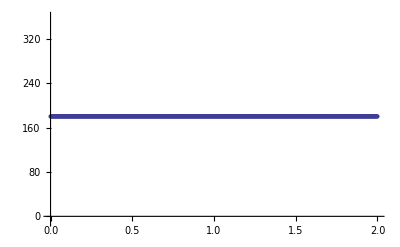

```mathematica
ListPlot[sp1,PlotRange-> {-10,360}] (* Mathematica function that draws the points corresponding to the list *)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve joining the points corresponding to the previous list is drawn.This function will be the only one used in the rest of the notebook to construct graphics. The user can obtain the graphic with the points for any list, introducing the Mathematica function “ListPlot” in the corresponding place.

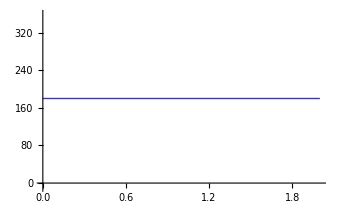

```mathematica
ListLinePlot[sp1,PlotRange-> {-10,360}]
```

## Plotting the plunge (theta) of the corresponding principal direction vs the linear parameter.

```mathematica
selector=2; (*for selecting theta *)
thetaSeqRad=selectArgument[anglesfirstVectorSeq,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
thetaSeq=radianSeqToDegreeSeq[thetaSeqRad];
```

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2};
```

```mathematica
sp2=putOneSequence[thetaSeq,interval]; (*sp1 allows us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

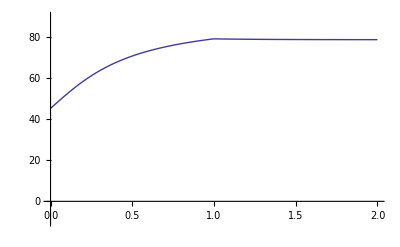

```mathematica
ListLinePlot[sp2, PlotRange-> {-10,90}] (* Mathematica function *)
```

## Sequence of principal axes ratios

This section obtains the  sequence of the three ratios of the principal axes of the strain ellipsoid {R13, R12, R23} and the area changes (Afinal/Ainitial) in the principal sections of the ellipsoid {A13, A12, A23}:

```mathematica
SeqR13R12R23A=computeSeqR13R12R23A[F];
```

selector: 1 for R13 (sqrtlambda1/sqrtlambda3)
  selector: 2 for R12 (sqrtlambda1/sqrtlambda2)
  selector: 3 for R23 (sqrtlambda2/sqrtlambda3)
  selector: 4 for A13 (area change in the plane 13: sqrtlambda1*sqrtlambda3)
  selector: 5 for A12 (area change in the plane 12: sqrtlambda1*sqrtlambda2)
  selector: 6 for A23 (area change in the plane 23: sqrtlambda2*sqrtlambda3)

```mathematica
selector=1;
seqR13=selectArgument[SeqR13R12R23A,selector];
```

```mathematica
selector=2;
seqR12=selectArgument[SeqR13R12R23A,selector];
```

```mathematica
selector=3;
seqR23=selectArgument[SeqR13R12R23A,selector];
```

```mathematica
selector=4;
seqA13=selectArgument[SeqR13R12R23A,selector];
```

```mathematica
selector=5;
seqA12=selectArgument[SeqR13R12R23A,selector];
```

```mathematica
selector=6;
seqA23=selectArgument[SeqR13R12R23A,selector];
```

## Sequence of volume changes

This section obtains the a sequence of the volume changes of the accumulated gradients from an incremental gradient sequence

```mathematica
volumeChangeSeq=computeSeqVolumeChange[F];
```

## To show the variation of any of these parameters against the lineal parameter

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2};(*It allows us to select the abscisa values *)
```

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
spA=putOneSequence[seqA13,interval];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

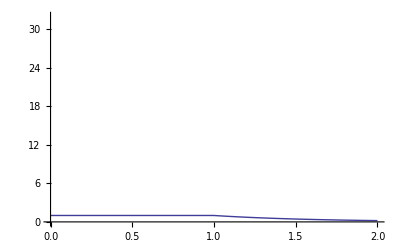

```mathematica
ListLinePlot[spA, PlotRange-> {0,32}] (* Mathematica function *)
```

## APLICATION OF THE DEFORMATION TO THE PLANE

## Applying a gradient to a plane

The composite sequence F acts over the initial plane base0 :
(It results a sequence of complex lists, from which the different parameters of the plane can be obtained applying the approppriate selector )

```mathematica
planeSeq=progressivePlaneTransform[F,base0];
```

## ORIENTATION OF THE DEFORMED PLANE

StrainModeler extracts a sequence of normal vectors to the planes (images of the original plane)

```mathematica
selector=7;
normalVectorSeq=selectArgument[planeSeq,selector];
```

```mathematica
Vg=fromNormalVectorSeqToAngleSeq[normalVectorSeq];
Vgpolo=fromVectorSeqToAngleSeq[normalVectorSeq];
```

# DIP DIRECTION (ALFA)

```mathematica
selector=1;
alphaSeqRad=selectArgument[Vg,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
alphaSeq=radianSeqToDegreeSeq[alphaSeqRad];
```

## Plotting alpha in degrees vs the linear parameter

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[alphaSeq,interval]; (*sp1 allows us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

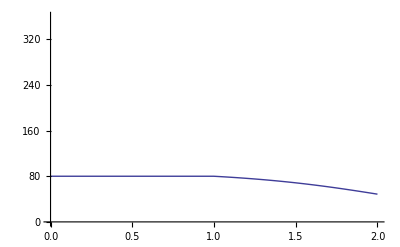

```mathematica
ListLinePlot[sp1, PlotRange-> {0,360}] (* Mathematica function *)
```

## Plotting the plunge direction (alpha) against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13alphaSeq=putTwoSequences[seqR13,alphaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

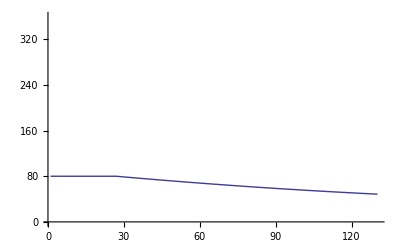

```mathematica
ListLinePlot[seqR13alphaSeq,PlotRange-> {0,360}](* Mathematica function *)
```

## DIP (THETA)

```mathematica
selector=2;
thetaSeqRad=selectArgument[Vg,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
thetaSeq=radianSeqToDegreeSeq[thetaSeqRad];
```

## Plotting theta vs the linear parameter

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[thetaSeq,interval]; (*sp1 allows us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

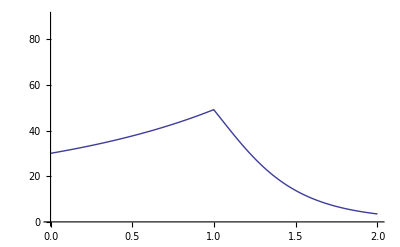

```mathematica
ListLinePlot[sp1, PlotRange-> {0,90}] (* Mathematica function *)
```

## Plotting the plunge (theta) against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, only the first argument can be changed by the user. It can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13thetaSeq=putTwoSequences[seqR13,thetaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

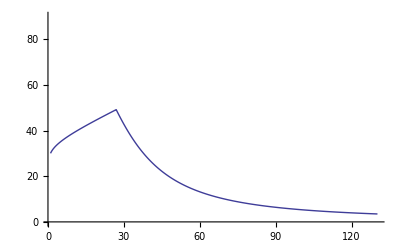

```mathematica
ListLinePlot[seqR13thetaSeq,PlotRange-> {0,90}](* Mathematica function *)
```

## DIP DIRECTION (ALFA) OF THE POLE TO THE TRANSFORMED PLANE

```mathematica
selector=1;
alphaSeqRadpolo=selectArgument[Vgpolo,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
alphaSeqpolo=radianSeqToDegreeSeq[alphaSeqRad];
```

## DIP (THETA) OF THE POLE TO THE TRANSFORMED PLANE

```mathematica
selector=2;
thetaSeqRadpolo=selectArgument[Vgpolo,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
thetaSeqpolo=radianSeqToDegreeSeq[thetaSeqRadpolo];
```

## PLOT OF THE PATH OF POLES TO THE PLANES IN THE EQUAL-AREA NET Plot of the line of directions corresponding to the pole to the plane in the template

This section draws the path described by the deformation of the pole to the plane in a polar equal-area net 
Introduce the desired values for the linear parameter. By default, it is from 0 to 2.

```mathematica
interval={0,2};
```

```mathematica
n=Dimensions[thetaSeqRad][[1]]; (* n is obtained calculating the number of elements in a list of angles *)
paramSeq=generateLinParameterSeq[interval,n];
```

```mathematica
parCurveSeq=genParametrizedCurveSeq[paramSeq,alphaSeqRadpolo,thetaSeqRadpolo];
```

## Choose between two possibilities to add information to the curve: - Tics without a label

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=100;
```

```mathematica
curveWithTics=putCurve[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.330551,0.661102,0.991653,1.3222,1.65275,1.98331}

## - Tics with a label indicating the value of the linear parameter

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=100;
```

```mathematica
curveWithTics=putCurveWithLabels[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.330551,0.661102,0.991653,1.3222,1.65275,1.98331}

Here the curve is drawn without the net:

```mathematica
Graphics[curveWithTics];
```

Data to personalize the net. These data could be changed by the user, but by default the most adequate are displayed:

```mathematica
degrees=Pi/180.;
deltaTheta=10 degrees;
smallDeltaTheta=2 degrees;
deltaAlpha=10 degrees;
smallDeltaAlpha=2 degrees;
(* Absolute thickness *)
thin=0.25;
thick=0.35;
(* Gray levels *)
clear=0.75;
dark=0.35;
```

The graphic elements to draw the net are generated:

```mathematica
eqAreaTemplate=generatesTemplate[deltaTheta, smallDeltaTheta, deltaAlpha, smallDeltaAlpha, thin, thick,clear,dark ];
```

The curve and the net are drawn together:

```mathematica
plotCurveAndTemplate[curveWithTics,eqAreaTemplate]
```

-Graphics-

## PARAMETERS OF THE STRAIN ELLIPSE ON THE DEFORMED PLANE Selector = 2 gives the magnitude of the major semiaxis Selector = 3 gives the magnitude of the minor semiaxis Selector = 4 gives R, the semiaxes ratio (major semiaxis/minor semiaxis)

Introduce the number corresponding to the desired selector

```mathematica
selector=4;
```

```mathematica
greatestAxisNormSeq=selectArgument[planeSeq,selector];
```

## Graphic vs the linear parameter

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[greatestAxisNormSeq,interval];(*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

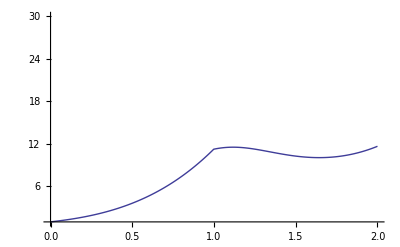

```mathematica
ListLinePlot[sp1,PlotRange-> {1,30}] (* Mathematica function *)
```

## Graphic against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqGratestAxisNormVsR13=putTwoSequences[seqR13,greatestAxisNormSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

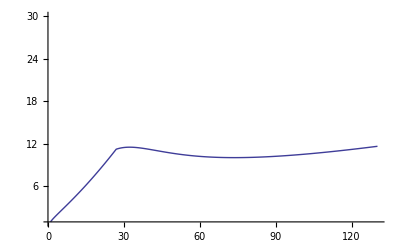

```mathematica
ListLinePlot[seqGratestAxisNormVsR13,PlotRange-> {1,30}] (* Mathematica function *)
```

## AREA CHANGE IN THE DEFORMED PLANE

```mathematica
planeSeq=progressivePlaneTransform[F,base0];
```

```mathematica
selector=9;
ProductoNorm1Norm2=selectArgument[planeSeq,selector];
```

## Graphic of the area change against the linear parameter

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[ProductoNorm1Norm2,interval]; (*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

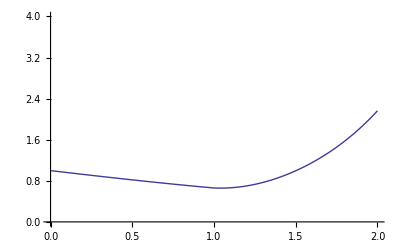

```mathematica
ListLinePlot[sp1,PlotRange-> {0,4}] (* Mathematica function *)
```

## Graphic against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqGratestAxisNormVsR13=putTwoSequences[seqR13,ProductoNorm1Norm2];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

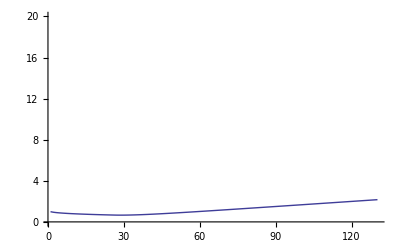

```mathematica
ListLinePlot[seqGratestAxisNormVsR13,PlotRange-> {0,20}] (* Mathematica function *)
```

## ORIENTATION OF THE AXES OF THE STRAIN ELLIPSE ON THE DEFORMED PLANE Selector = 5 gives the major axis Selector = 6 gives the minor axis

Introduce the number corresponding to the desired selector

```mathematica
selector=5;
```

```mathematica
principalVector1Seq=selectArgument[planeSeq,selector];
```

The vector sequence principalVector1Seq is translated to geological angles {alpha, theta}:

```mathematica
V1g=fromVectorSeqToAngleSeq[principalVector1Seq];
```

# PLUNGE DIRECTION (ALFA)

## Plotting alpha in degrees vs the linear parameter

```mathematica
selector=1;
alphaSeqRad=selectArgument[V1g,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
alphaSeq=radianSeqToDegreeSeq[alphaSeqRad];
```

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[alphaSeq,interval]; (*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

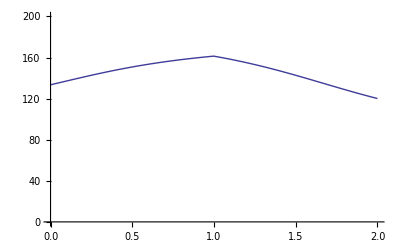

```mathematica
ListLinePlot[sp1,PlotRange-> {0,200}] (* Mathematica function *)
```

## Graphic of alpha against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13alphaSeq=putTwoSequences[seqR13,alphaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

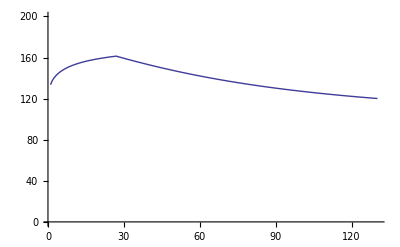

```mathematica
ListLinePlot[seqR13alphaSeq,PlotRange-> {0,200}](* Mathematica function *)
```

## PLUNGE (THETA) Plotting theta vs the linear parameter

```mathematica
selector=2;
thetaSeqRad=selectArgument[V1g,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
thetaSeq=radianSeqToDegreeSeq[thetaSeqRad];
```

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[thetaSeq,interval]; (*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

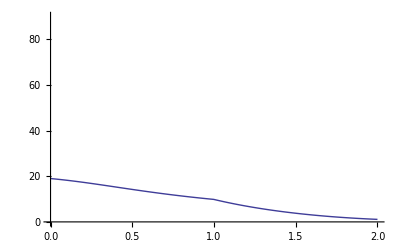

```mathematica
ListLinePlot[sp1,PlotRange-> {0,90}] (* Mathematica function *)
```

## Graphic of theta against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, only the first argument can be changed by the user. It can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13thetaSeq=putTwoSequences[seqR13,thetaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

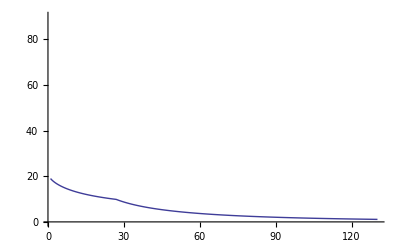

```mathematica
ListLinePlot[seqR13thetaSeq,PlotRange-> {0,90}](* Mathematica function *)
```

## Plot of the line of directions in the template

This section draws the path described by the deformation of the chosen axis of the strain ellipsoid in a polar equal-area net 
Introduce the desired values for the linear parameter. By default, it is from 0 to 2.

```mathematica
interval={0,2};
```

```mathematica
n=Dimensions[thetaSeqRad][[1]]; (* n is obtained calculating the number of elements in a list of angles *)
paramSeq=generateLinParameterSeq[interval,n];
```

```mathematica
parCurveSeq=genParametrizedCurveSeq[paramSeq,alphaSeqRad,thetaSeqRad];
```

## Choose between two possibilities to add information to the curve: - Tics without a label

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=200;
```

```mathematica
curveWithTics=putCurve[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.664441,1.32888,1.99332}

## - Tics with a label indicating t value

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=200;
```

```mathematica
curveWithTics=putCurveWithLabels[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.664441,1.32888,1.99332}

Here the curve is drawn without the net:

```mathematica
Graphics[curveWithTics];
```

Data to personalize the net. These data could be changed by the user, but by default the most adequate are displayed:

```mathematica
degrees=Pi/180.;
deltaTheta=10 degrees;
smallDeltaTheta=2 degrees;
deltaAlpha=10 degrees;
smallDeltaAlpha=2 degrees;
(* Absolute thickness *)
thin=0.25;
thick=0.35;
(* Gray levels *)
clear=0.75;
dark=0.35;
```

The graphic elements to draw the net are generated:

```mathematica
eqAreaTemplate=generatesTemplate[deltaTheta, smallDeltaTheta, deltaAlpha, smallDeltaAlpha, thin, thick,clear,dark ];
```

The curve and the net are drawn together:

```mathematica
a1=plotCurveAndTemplate[curveWithTics,eqAreaTemplate]
```

-Graphics-

## PARAMETERS OF THE AXIAL PLANE OF FOLDS FORMED IN THE DEFORMED PLANE In this section it is assumed that the shortening of the deformed plane involves the development of folds, whose axial plane contains the major axis of the finite strain ellipse on the plane and is perpendicular to the deformed plane.

```mathematica
selector=8;
normalVectorSeq=selectArgument[planeSeq,selector];
```

```mathematica
Vg=fromNormalVectorSeqToAngleSeq[normalVectorSeq];
Vgpolo=fromVectorSeqToAngleSeq[normalVectorSeq];
```

## DIP DIRECTION (ALFA) Plotting alpha in degrees vs the linear parameter

```mathematica
selector=1;
alphaSeqRad=selectArgument[Vg,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
alphaSeq=radianSeqToDegreeSeq[alphaSeqRad];
```

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[alphaSeq,interval]; (*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

```mathematica
ListLinePlot[sp1,PlotRange-> {50,200}] (* Mathematica function *)
```

-Graphics-

## Plotting the dip direction (alpha) against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, the first argument can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13alphaSeq=putTwoSequences[seqR13,alphaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

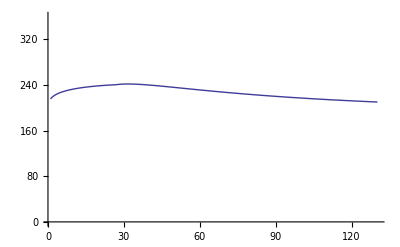

```mathematica
ListLinePlot[seqR13alphaSeq,PlotRange-> {0,360}](* Mathematica function *)
```

## DIP (THETA)

## Plotting theta vs the linear parameter

```mathematica
selector=2;
thetaSeqRad=selectArgument[Vg,selector];
```

StrainModeler translates the sequence of angles in radians to angles in degrees:

```mathematica
thetaSeq=radianSeqToDegreeSeq[thetaSeqRad];
```

Introduce the desired values for the linear parameter (abscisa values). By default, it is from 0 to 2.

```mathematica
interval={0,2}; (*It allows us to select the abscisa values *)
```

```mathematica
sp1=putOneSequence[thetaSeq,interval]; (*sp1 allow us make the desired plot*)
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

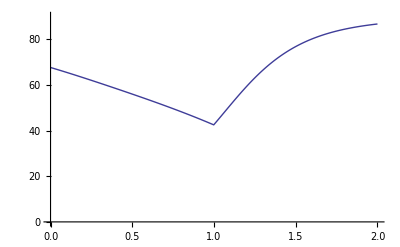

```mathematica
ListLinePlot[sp1,PlotRange-> {0,90}] (* Mathematica function *)
```

## Plotting the plunge (theta) against a parameter of the strain ellipsoid (R13, R12 or R23, A13, A12, A23 or volume change)

In the following input, only the first argument can be changed by the user. It can be seqR13, seqR12, seqR23, seqA13, seqA12, seqA23 or volumeChangeSeq

```mathematica
seqR13thetaSeq=putTwoSequences[seqR13,thetaSeq];
```

In the following input, the interval of the ordinate scale can be chosen. Then, the graphic of the curve corresponding to the previous list is drawn.

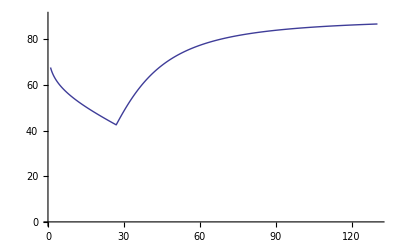

```mathematica
ListLinePlot[seqR13thetaSeq,PlotRange-> {0,90}](* Mathematica function *)
```

## DIP DIRECTION (ALFA) OF THE POLE TO THE AXIAL PLANE OF THE FOLDS FORMED IN THE TRANSFORMED PLANE

```mathematica
selector=1;
alphaSeqRadpolo=selectArgument[Vgpolo,selector];
```

```mathematica
alphaSeqpolo=radianSeqToDegreeSeq[alphaSeqRad];
```

## DIP (THETA) OF THE POLE TO THE AXIAL PLANE OF THE FOLDS FORMED IN THE TRANSFORMED PLANE

```mathematica
selector=2;
thetaSeqRadpolo=selectArgument[Vgpolo,selector];
```

```mathematica
thetaSeqpolo=radianSeqToDegreeSeq[thetaSeqRadpolo];
```

## Plot of the poles to the axial plane in the template

This section draws the path described by the deformation of the direction in a polar equal-area net 
Introduce the desired values for the linear parameter. By default, it is from 0 to 2.

```mathematica
interval={0,2};
```

```mathematica
n=Dimensions[thetaSeqRad][[1]]; (* n is obtained calculating the number of elements in a list of angles *)
paramSeq=generateLinParameterSeq[interval,n];
```

```mathematica
parCurveSeq=genParametrizedCurveSeq[paramSeq,alphaSeqRadpolo,thetaSeqRadpolo];
```

## Choose between two possibilities to add information to the curve: - Tics without a label

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=200;
```

```mathematica
curveWithTics=putCurve[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.664441,1.32888,1.99332}

## - Tics with a label indicating t value

Introduce the desired number of points separating two tics, obviously p must be less than n1+n2.

```mathematica
p=200;
```

```mathematica
curveWithTics=putCurveWithLabels[parCurveSeq,p];
```

Parameter Tic Values:{0.,0.664441,1.32888,1.99332}

Here the curve is drawn without the net:

```mathematica
Graphics[curveWithTics];
```

Data to personalize the net. These data could be changed by the user, but by default the most adequate are displayed:

```mathematica
degrees=Pi/180.;
deltaTheta=10 degrees;
smallDeltaTheta=2 degrees;
deltaAlpha=10 degrees;
smallDeltaAlpha=2 degrees;
(* Absolute thickness *)
thin=0.25;
thick=0.35;
(* Gray levels *)
clear=0.75;
dark=0.35;
```

The graphic elements to draw the net are generated:

```mathematica
eqAreaTemplate=generatesTemplate[deltaTheta, smallDeltaTheta, deltaAlpha, smallDeltaAlpha, thin, thick,clear,dark ];
```

The curve and the net are drawn together:

```mathematica
plotCurveAndTemplate[curveWithTics,eqAreaTemplate]
```

-Graphics-